# Macrophyte’s adaptive dynamics in a shallow lake

This notebook is used to determine the values of the evolutionary singularities of a macrophyte population whose depth in a lake can evolve. 
For each scenario, a .txt file containing the evolutionary singularities for a range of u and w parameters is created. The latter can be used to generate the E3-diagrams and 2D plots of Figure 3.

### Sets of parameters used

These are the parameters used in the 3 scenarios of eco-evolutionary dynamics of macrophytes. 
Scenario 1: depth is associated to a trade-off between light and nutrient, no asymmetry in light competition (b=0), no priority effect (p=0)
Scenario 2: trade-off + asymmetry (b=1) + no priority (p=0)
Scenario 3: trade-off + asymmetry (b=1) + priority (b=0.5)
parameters u and w are not specified since we study the effect of their variation on evolutionary outcomes.

```mathematica
scenario1 = {W0 -> 1, a0-> 0.01, zb -> 10, r -> 0.5, l -> 0.05, b->0,  q0->0.05, p->0,h->0.1, Nu0->5 }
```

{W0→1,a0→0.01,zb→10,r→0.5,l→0.05,b→0,q0→0.05,p→0,h→0.1,Nu0→5}

```mathematica
scenario2 = {W0 -> 1, a0-> 0.01, zb -> 10, r -> 0.5, l -> 0.05, b->1,  q0->0.05, p->0,h->0.1, Nu0->5 }
```

{W0→1,a0→0.01,zb→10,r→0.5,l→0.05,b→1,q0→0.05,p→0,h→0.1,Nu0→5}

```mathematica
scenario3 = {W0 -> 1, a0-> 0.01, zb -> 10, r -> 0.5, l -> 0.05, b->1,  q0->0.005, p->0.5,h->0.1, Nu0->5 }
```

{W0→1,a0→0.01,zb→10,r→0.5,l→0.05,b→1,q0→0.005,p→0.5,h→0.1,Nu0→5}

### Model equations

```mathematica
grS = (r S (n/(n+h)) (1/(1+ a[z,z] S + W[z])) - l S )/.{n -> Nu[z]/(1+q[z] S)}//FullSimplify
```

-l S+(r S Nu[z])/((h+Nu[z]+h S q[z]) (1+S a[z,z]+W[z]))

```mathematica
reseq = Solve[grS ==0, S]
```

{{S→0},{S→1/(2 h l a[z,z] q[z])(-h l a[z,z]-l a[z,z] Nu[z]-h l q[z]-h l q[z] W[z]+√(4 h l a[z,z] q[z] (-h l-l Nu[z]+r Nu[z]-h l W[z]-l Nu[z] W[z])+(-h l a[z,z]-l a[z,z] Nu[z]-h l q[z]-h l q[z] W[z])^2))},{S→-1/(2 h l a[z,z] q[z])(h l a[z,z]+l a[z,z] Nu[z]+h l q[z]+h l q[z] W[z]+√(4 h l a[z,z] q[z] (-h l-l Nu[z]+r Nu[z]-h l W[z]-l Nu[z] W[z])+(-h l a[z,z]-l a[z,z] Nu[z]-h l q[z]-h l q[z] W[z])^2))}}

### Feasibility conditions

Under which conditions are each equilibria feasible ? 
Since every parameter is positive, the third solution is necessarily negative. 
In the second solution, what is inside the square root has to be positive for the macrophyte population to be real, which is the case when :

```mathematica
Solve[(-h l-l Nu+r Nu-h l W-l Nu W)==0, Nu]//FullSimplify
```

{{Nu→-(h l (1+W))/(l-r+l W)}}

Since Nu is a quantity of nutrient it also has to be positive, which is the case when r>l(1+W).
The feasibility conditions are :  Nu > h l (1 + W) / (r - l (1+W)),  r>l(1+W).

### Invasion fitness

The invasion fitness of the mutant can be written as :

```mathematica
invasionFitness = (r (n/(n+h)) (1/(1+ a[zm,z] Seq + W[zm])) - l)/.{n-> Nu[zm]/(1+q[z] Seq)}//Simplify
```

-l+(r Nu[zm])/((h+Nu[zm]+h Seq q[z]) (1+Seq a[zm,z]+W[zm]))

Assuming that the resident has reached equilibrium, it becomes:

```mathematica
invasionFitness = invasionFitness/.{Seq -> S/.reseq[[2]]}
```

-l+(r Nu[zm])/((h+Nu[zm]+1/(2 l a[z,z])(-h l a[z,z]-l a[z,z] Nu[z]-h l q[z]-h l q[z] W[z]+√(4 h l a[z,z] q[z] (-h l-l Nu[z]+r Nu[z]-h l W[z]-l Nu[z] W[z])+(-h l a[z,z]-l a[z,z] Nu[z]-h l q[z]-h l q[z] W[z])^2))) (1+1/(2 h l a[z,z] q[z])a[zm,z] (-h l a[z,z]-l a[z,z] Nu[z]-h l q[z]-h l q[z] W[z]+√(4 h l a[z,z] q[z] (-h l-l Nu[z]+r Nu[z]-h l W[z]-l Nu[z] W[z])+(-h l a[z,z]-l a[z,z] Nu[z]-h l q[z]-h l q[z] W[z])^2))+W[zm]))

### Specification of the functions used

Mechanism 1: vertical trade-off between light and nutrient

```mathematica
Nu[x_]:=(Nu0/(u* Sqrt[2 * Pi])) * Exp[-(zb-x)^2/(2u^2)]
```

```mathematica
W[x_]:=  W0 Exp[w x] - W0
```

Mechanism 2: asymmetric competition by shading

```mathematica
a[x_,y_] := (a0 2 Exp[ b (x-y)] / (1 +  Exp[b (x-y)]))
```

Mechanism 3: priority access to nutrient

```mathematica
q[x_] := (q0 Exp[p x] )
```

### Feasibility set of parameters

Recall that Nu needs to be greater than  h l (1 + W) / (r - l (1+W)). 
We can test : 		Nu - h l (1 + W) / (r - l (1+W)) > 0  with  (r - l (1+W)) > 0 
or , since Nu >0, 	0 < (h l (1 + W) / (r - l (1+W)))/Nu < 1

```mathematica
feasibilityCondition =(h l (1 + W[z]) / (r - l (1+W[z])))/Nu[z]
```

(ⅇ^((-z+zb)^2/(2 u^2)) h l √(2 π) u (1-W0+ⅇ^(w z) W0))/(Nu0 (r-l (1-W0+ⅇ^(w z) W0)))

## PIPs

This section of the file generates the PIPs presented in Fig. 3 and can be used to generate others with different sets of parameters.

```mathematica
base = ContourPlot[z^2 + zm^2,{z,0,10},{zm,0,10}, Contours-> 0, ContourShading->{Blue},PlotPoints->5];
```

### First scenario

{z→2.31916}

{z→6.91846}

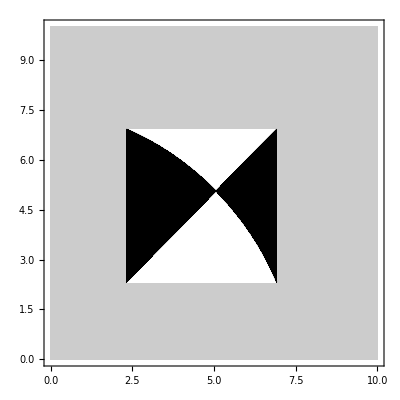

```mathematica
example1 = Join[scenario1, {u->3, w->0.3}]; (*for strong light attenuation and little nutrient diffusion*)
zmin = FindRoot[((feasibilityCondition/.example1)-1), {z,0}] (*find the boundaries of feasible depths*)
zmax = FindRoot[((feasibilityCondition/.example1)-1), {z,10}]
If[(z/.zmin) < 0, zmin = 0, zmin = (z/.zmin)];
If[(z/.zmax) > 10, zmax = 10, zmax= (z/.zmax)];
plot = ContourPlot[invasionFitness/.example1,{z,zmin,zmax},{zm,zmin,zmax}, Contours-> {0}, ContourShading->{White, Black},PlotPoints->50]; (*draw the PIP in the feasible depths - black regions correspond to a positive invasion fitness, white regions to negative invasion fitness*)
Show[base,plot]
```

### Second scenario

{z→-4.51957}

{z→17.4586}

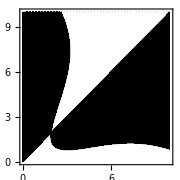

```mathematica
example2 = Join[scenario2, {u->5.1, w->0.1}];
zmin = FindRoot[((feasibilityCondition/.example2)-1), {z,0}]
zmax = FindRoot[((feasibilityCondition/.example2)-1), {z,10}]
If[(z/.zmin) < 0, zmin = 0, zmin = (z/.zmin)];
If[(z/.zmax) > 10, zmax = 10, zmax= (z/.zmax)];
plot = ContourPlot[invasionFitness/.example2,{z,zmin,zmax},{zm,zmin,zmax}, Contours-> {0}, ContourShading->{White, Black},PlotPoints->50];
Show[base,plot, ImageSize->Small]
```

### Third scenario

{z→-3.00595}

{z→13.5585}

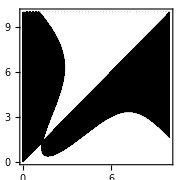

```mathematica
example3 = Join[scenario3, {u->4.5, w->0.15}];
zmin = FindRoot[((feasibilityCondition/.example3)-1), {z,0}]
zmax = FindRoot[((feasibilityCondition/.example3)-1), {z,10}]
If[(z/.zmin) < 0, zmin = 0, zmin = (z/.zmin)];
If[(z/.zmax) > 10, zmax = 10, zmax= (z/.zmax)];
plot = ContourPlot[invasionFitness/.example3,{z,zmin,zmax},{zm,zmin,zmax}, Contours-> {0}, ContourShading->{White, Black},PlotPoints->50];
Show[base,plot, ImageSize->Small]
```

## Evolutionary singularity analysis

### What is the value of the evolutionary singularity ?

For which z does ds/dzm (z, z) = 0 ?

```mathematica
dsdzm = D[invasionFitness, zm] ;
```

### Is the singularity non-invasible ?

<-> d2s/dzm2 (z*, z*) < 0 ?

```mathematica
stabilityCondition = D[dsdzm, zm]/.{z -> ES, zm -> ES};
```

### Is the equilibrium attractive ?

<-> d2s/dzm2(z*,z*) + d2s/dzdzm(z*,z*) <0

```mathematica
secondPart =  D[invasionFitness, z] ;
```

```mathematica
secondPart = D[secondPart, zm];
```

```mathematica
secondPart = secondPart/.{z -> ES, zm -> ES};
```

```mathematica
attractivityCondition = stabilityCondition + secondPart
```

-(ⅇ^(ES w-(1)^2/(2 u^2)) Nu0 r w^2 W0)/(√(2 π) u (h+(ⅇ^1 Nu0)/(√(2 π) u)+(7+√(1^2+1))/(2 a0 l)) (1-W0+ⅇ^ES11 W0+(ⅇ^1 (1))/(2 h l q0))^2)+21
 |  |  |  |

## Obtaining values for E3 diagrams or 2D plots

This part of the file computes the value of the evolutionary singularity and classifies it according to convergence and invasibility criteria for a range of nutrient diffusion u and light attenuation w values. The output is written in a txt file in the data/ directory.

```mathematica
filename = ParentDirectory[NotebookDirectory[]]<>"/data/evolution_scenario1.txt";(*or scenario2 or scenario3*)
```

```mathematica
file = OpenWrite[filename, FormatType->StandardForm]
```

OutputStream[…]

```mathematica
pars = scenario1 (*or pars=scenario2 or pars=scenario3*)
```

{W0→1,a0→0.01,zb→10,r→0.5,l→0.05,b→0,q0→0.05,p→0,h→0.1,Nu0→5}

```mathematica
Write[file, "#"<>ToString[pars]]
```

```mathematica
Write[file, "u, w, zmin, zmax, ES, type"]
```

```mathematica
Do[
(*find the feasibility range: 
- is there an upper-bound and a lower bound, or only one, or no bound? *)
lim= z/.FindRoot[((feasibilityCondition/.pars)-1), {z,#}]&/@Range[10];
lim=N[Round[1000000 lim ]/1000000];
lim=DeleteDuplicates[lim];
lim=DeleteCases[lim, x_ /; (x<0 ||  x>10) ];
If[Length[lim]==2,zmin=lim[[1]]; zmax=lim[[2]] ];
If [Length[lim]==0,zmin=0; zmax=10];(*This can also possilby be that life is possible nowhere (but that case is delt with below)*)
If [Length[lim]==1,If[(((feasibilityCondition/.pars)-1)/.{z -> lim-1})[[1]]<0,zmax=lim[[1]];zmin=0, zmin=lim[[1]];zmax=10]];

ES = z/.(FindRoot[dsdzm/.pars/.{zm -> z},{z,zmin}]); (*compute the evolutionary singularity*)
(*Classify the evolutionary singularity :*) 
If[(feasibilityCondition/.pars/.{z->ES}) < 0 || (feasibilityCondition/.pars/.{z->ES}) >1, eType= "Unfeasible",
If[ES> zmin &&ES<zmax,

	If[((attractivityCondition/.pars) < 0  )&& ((stabilityCondition/.pars)< 0 ), 
	eType = "CSS"];
	If[((attractivityCondition/.pars) < 0  )&& ((stabilityCondition/.pars)> 0 ),
	eType = "Branching point"];
	If[((attractivityCondition/.pars) > 0  )&& ((stabilityCondition/.pars)> 0 ), 
	eType ="Repellor"];
	If[((attractivityCondition/.pars) > 0  )&& ((stabilityCondition/.pars)< 0 ), 
	eType ="Garden of Eden"],
 eType="No ES"]];
(*if there is no evolutionary singularity (lines in the PIP do not cross), does the macrophyte population evolve towards the bottom or the surface of the lake ? : *)
If[eType=="No ES", If[(invasionFitness/.pars/.{z->0,zm->0.001})<0,ES=zmin,ES=zmax]];
Write[file,u,",",w,"," , zmin,"," ,zmax,"," ,ES,"," ,eType];

, {u,1,7,0.05},{w,0,0.7,0.005}]
```

```mathematica
Close[file];
```